```mathematica
d1[T_]:=d0*Tanh[1.74*√(Tc/T-1)]
d0=0.33;Tc=4.1;h=4.135667662;T=.1;d=d0*1.21306
 h*0.3/2
```

0.40031

0.62035

```mathematica
phi[k_,w_]:=(EllipticE[k]-(1-k) EllipticK[k])/((1+k)^2 √((1+k)^2-((h w)/(2 d))^2 (1-k^2)))
A[w_]:=NIntegrate[(EllipticE[k]-(1-k) EllipticK[k])/((1+k)^2 √Abs[(1+k)^2-((h w)/(2 d))^2 (1-k^2)]),{k,(h w-2 d)/(h w+2 d),1}]
B[w_]:=NIntegrate[(EllipticE[k]-(1-k) EllipticK[k])/((1+k)^2 √Abs[(1+k)^2-((h w)/(2 d))^2 (1-k^2)]),{k,0,1}]
signorm[w_]:=((8 h w) (UnitStep[h w-2 d] A[w]+UnitStep[-h w+2 d] B[w]))/(2 π d)
```

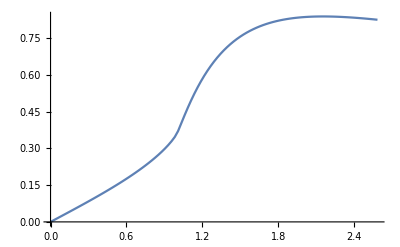

```mathematica
data=Table[{h*w/(2*d),signorm[w]},{w,0.,.5,0.005}] ;ListPlot[{data},PlotRange->All,Joined->True]
```

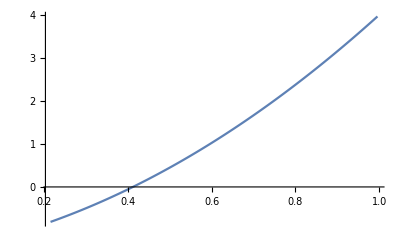

```mathematica
data=Table[{k,(1+k)^2-((h .3)/(2 d))^2 (1-k^2)},{k,(h .3-2 d)/(h .3+2 d),1,0.005}] ;ListPlot[{data},PlotRange->All,Joined->True]
```